## Mathematica Demonstration

All code written by myself and is available at: https://github.com/wilson-nunn/mathematica_sigs_tensor_algebra

## Setup

### Parameters

```mathematica
d=1;m=5;lim1={-5,-4};lim2={-1/2,1/2};lim3={4,5};lims={Min[Flatten[{lim1,lim2,lim3}]],Max[Flatten[{lim1,lim2,lim3}]]}
```

{-5,5}

```mathematica
vars=PolynomialVars[d];
monomials=Monomials[m,d];
```

```mathematica
{evals1,efuncs1}=LinearMappingBasisFunctions[m,d,lim1,lims];
{evals2,efuncs2}=LinearMappingBasisFunctions[m,d,lim2,lims];
{evals3,efuncs3}=LinearMappingBasisFunctions[m,d,lim3,lims];
```

#### Computing Basis Functions

```mathematica
η=Chebyshevs[m,lims,d];
η
```

{1,x1/5,-1+(2 x1^2)/25,-(3 x1)/5+(4 x1^3)/125,1-(8 x1^2)/25+(8 x1^4)/625,x1-(4 x1^3)/25+(16 x1^5)/3125}

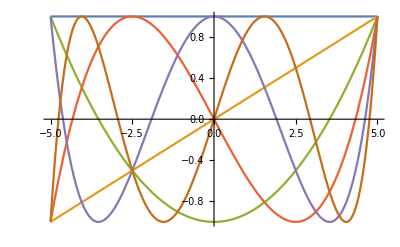

```mathematica
Plot[η,Join[vars,lims]]
```

```mathematica
matrixA=ParallelTable[NewIntegrate[(i*j),lim1[[1]],lim1[[2]],d],{i,η},{j,η}];
matrixB=ParallelTable[NewIntegrate[(i*j),lims[[1]],lims[[2]],d],{i,η},{j,η}];
```

```mathematica
eigenSystem=Eigensystem@(N[Inverse[matrixA].matrixB]);
eigenSystem[[2]]=eigenSystem[[2]].η;
```

```mathematica
eigenSystem//Simplify
```

{{3.58805×10^15,3.08078×10^10,2.16886×10^6,923.337,4.42955,1.49327},{0.0441813+0.0493459 x1+0.0220151 x1^2+0.00490413 x1^3+0.000545474 x1^4+0.0000242354 x1^5,-0.439377-0.285915 x1-0.0362174 x1^2+0.0122463 x1^3+0.00361531 x1^4+0.000260343 x1^5,-1.13325+0.0345367 x1+0.239393 x1^2+0.024192 x1^3-0.00924956 x1^4-0.00132155 x1^5,0.0465185+0.85371 x1-0.129854 x1^2-0.111273 x1^3+0.00626856 x1^4+0.00336511 x1^5,0.288-0.463815 x1-0.137517 x1^2+0.104879 x1^3+0.005511 x1^4-0.00384769 x1^5,-0.075872+0.0698609 x1+0.0500404 x1^2-0.0204165 x1^3-0.00357557 x1^4+0.00110608 x1^5}}

### Eigenfunctions

```mathematica
Plot[efuncs1,Join[vars,lims],PlotLegends->Automatic, GridLines->{Join[lim1,lim2,lim3], None},ImageSize->Medium]
```

### Generate Data

```mathematica
ClearAll[func];
func[x_]:=1/(1+x^2) ;
```

```mathematica
seed=947217;
SeedRandom[seed];
```

```mathematica
data1Raw=RandomReal[lim1,{20,d}];
data2Raw=RandomReal[lim2,{20,d}];
data3Raw=RandomReal[lim3,{3,d}];
```

```mathematica
data1=data1Raw+0*0.5*RandomVariate[NormalDistribution[0,1],Length[data1Raw]];
data2=data2Raw+0*0.5*RandomVariate[NormalDistribution[0,1],Length[data2Raw]];
data3=data3Raw+0*0.5*RandomVariate[NormalDistribution[0,1],Length[data3Raw]];
data=Join[data1,data2,data3];
```

```mathematica
y1=func@@@data1;
y2=func@@@data2;
y3=func@@@data3;
y=Join[y1,y2,y3];
```

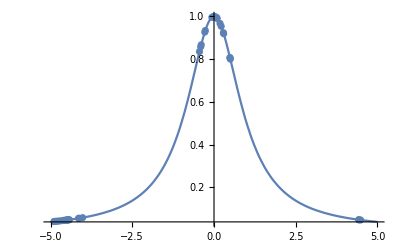

```mathematica
Show[Plot[func[x],Prepend[lims,x],PlotRange->All,GridLines->{Join[lim1,lim2,lim3],None}],ListPlot[MapThread[Append,{data1,y1}]],ListPlot[MapThread[Append,{data2,y2}]],ListPlot[MapThread[Append,{data3,y3}]]]
```

## Fit models

### Standard Least Squares

```mathematica
lmsMono=LinearModelFit[MapThread[Append,{data,y}],monomials,vars];
```

```mathematica
Show[Plot[func[x],Prepend[lims,x],PlotRange->All,GridLines->{Join[lim1,lim2,lim3],None},PlotStyle->Dashed],Plot[lmsMono[t],Prepend[lims,t],PlotStyle->{Orange}],ListPlot[MapThread[Append,{data,y}]](*,ImageSize->Medium*)]
```

### Robust Eigenvalue Polynomial Regression

#### Basis function selection

```mathematica
Reverse/@{evals1,evals2,evals3}
```

```mathematica
Cases[Table[Length/@(Cases[#,x_/;x≤k]&/@{evals1,evals2,evals3}),{k,Union@@{evals1,evals2,evals3}}],
		y_/;And[Not[MemberQ[y,0]],AllTrue[(Length/@{data1,data2,data3})-y,Not[Negative[#]]&]]]
```

```mathematica
eFuncSelections=(Table[{efuncs1,efuncs2,efuncs3}[[i,-#[[i]];;]],{i,Length[{efuncs1,efuncs2,efuncs3}]}]&/@Cases[Table[Length/@(Cases[#,x_/;x≤k]&/@{evals1,evals2,evals3}),{k,Union@@{evals1,evals2,evals3}}],
		y_/;And[Not[MemberQ[y,0]],AllTrue[(Length/@{data1,data2,data3})-y,Not[Negative[#]]&]]]);
Cases[Table[{i,Total[Length/@eFuncSelections[[i]]],MatrixRank[coefF/@Flatten[eFuncSelections[[i]]]]},
		{i,1,Length[eFuncSelections]}],x_/;x[[2]]≤x[[3]]][[All,1]]
```

#### Fit first model

```mathematica
basisFuncs=EigenFunctionSelection[{efuncs1,efuncs2,efuncs3},{evals1,evals2,evals3},{data1,data2,data3}];
basisFuncs[[2]]//Expand
```

```mathematica
step1SubModels=Table[LinearModelFit[MapThread[Append,{{data1,data2,data3}[[j]],{y1,y2,y3}[[j]]}],eFunc[[j]],vars,
		IncludeConstantBasis->False]@@PolynomialVars[d,"t"],{j,1,Length[{data1,data2,data3}]},{eFunc,basisFuncs}]//Expand
```

```mathematica
step1Models=Apply[Plus,#]&/@Transpose[PadRight[#,Max[Length/@step1SubModels],#[[-1]]]&/@step1SubModels]
step1Models=Function[Evaluate[PolynomialVars[d,"t"]],Evaluate[#]]&/@step1Models;
```

#### Iterate

```mathematica
residuals=Table[{y1,y2,y3}[[i]]-model@@@{data1,data2,data3}[[i]],{i,1,Length[{data1,data2,data3}]},{model,step1Models}];
```

```mathematica
correction1SubModels=Table[LinearModelFit[MapThread[Append,{{data1,data2,data3}[[j]],residuals[[j,i]]}],basisFuncs[[i,j]],vars,
		IncludeConstantBasis->False]@@PolynomialVars[d,"t"],{j,1,Length[{data1,data2,data3}]},{i,1,Length[basisFuncs]}]//Expand
```

```mathematica
correction1Models=Apply[Plus,#]&/@Transpose[PadRight[#,Max[Length/@correction1SubModels],#[[-1]]]&/@correction1SubModels]
```

```mathematica
step2Models=(step1Models[[#]]@@PolynomialVars[d,"t"]+correction1Models[[#]])&/@Range[1,Length[step1Models]]
```

#### All together

```mathematica
lmsEigens1=LinearModelsFirst[d,{data1,data2,data3},{y1,y2,y3},{efuncs1,efuncs2,efuncs3},{evals1,evals2,evals3}];
```

```mathematica
iterations=NestList[LinearModelsIteration[d,#,{data1,data2,data3},{y1,y2,y3},{efuncs1,efuncs2,efuncs3},{evals1,evals2,evals3}]&,lmsEigens1,100];
```

```mathematica
labels=EigenFunctionSelectionDisplay[{efuncs1,efuncs2,efuncs3},{evals1,evals2,evals3},{data1,data2,data3}];
Grid[Table[Table[Show[Plot[func[x],Prepend[lims,x],GridLines->{Join[lim1,lim2,lim3],None},PlotLabel->labels[[i]],PlotStyle->Dashed],Plot[(iterations[[j]])[[i]][t],Prepend[lims,t],PlotStyle->Orange]],{i,1,Length[iterations[[-1]]]}],{j,{1,2,5,10,50,100}}]]
```

### Analysis of Fitted Models

```mathematica
Sqrt[Total[(y-#@@@data)^2]]&/@Prepend[iterations[[-1]],lmsMono]
```

```mathematica
Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lims,x]]]&/@Prepend[iterations[[-1]],lmsMono]
```

```mathematica
{(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim1,x]]]&/@Prepend[iterations[[-1]],lmsMono])+(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim2,x]]]&/@Prepend[iterations[[-1]],lmsMono])+(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim3,x]]]&/@Prepend[iterations[[-1]],lmsMono])}
```

```mathematica
{(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim1,x]]]&/@Prepend[iterations[[-1]],lmsMono]),(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim2,x]]]&/@Prepend[iterations[[-1]],lmsMono]),(Sqrt[NIntegrate[(#[x]-func[x])^2,Prepend[lim3,x]]]&/@Prepend[iterations[[-1]],lmsMono])}
```

```mathematica
Show[Plot[func[x],Prepend[lims,x],PlotStyle->Dashed],
Plot[lmsMono[x],Prepend[lims,x],PlotStyle->Orange],
Plot[Through[iterations[[-1]][x]],Prepend[lims,x],PlotStyle->Green]]
```